### Start choosing the example:

```mathematica
t=13;
beta = 0;
A = 0.2;
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,0,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{{1,2,4,S1},{1,3,4,S2}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->10,U1->1,S1->900,S2->0}];//Timing
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.134502 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.164769,Null}

<|{1,1->2}→21,{1,1->3}→21,{2,2->4}→1,{3,3->4}→11,{4,4->ex6921}→1,{en6920,en6920->1}→21,{2,1->2}→21,{3,1->3}→11,{4,2->4}→1,{4,3->4}→1,{ex6921,4->ex6921}→1,{1,en6920->1}→21|>

<|{2,1->2}→0,{3,1->3}→10,{4,2->4}→0,{4,3->4}→10,{ex6921,4->ex6921}→10,{1,en6920->1}→10,{1,1->2}→0,{1,1->3}→0,{2,2->4}→0,{3,3->4}→0,{4,4->ex6921}→0,{en6920,en6920->1}→0|>

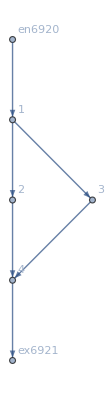

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j6922→0,j6923→10,j6924→0,j6925→10,j6926→10,j6927→10,j6928→0,j6929→0,j6930→0,j6931→0,j6932→0,j6933→0,jt6934→0,jt6935→0,jt6936→0,jt6937→0,jt6938→0,jt6939→10,jt6940→0,jt6941→0,jt6942→10,jt6943→0,jt6944→0,jt6945→0,jt6946→0,jt6947→10,jt6948→0,jt6949→0,u6950→21,u6951→21,u6952→1,u6953→11,u6954→1,u6955→21,u6956→21,u6957→11,u6958→1,u6959→1,u6960→1,u6961→21|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.70709×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.70709×10^-17

<|j6922→0,j6923→10,j6924→0,j6925→10,j6926→10,j6927→10,j6928→0,j6929→0,j6930→0,j6931→0,j6932→0,j6933→0,jt6934→0,jt6935→0,jt6936→0,jt6937→0,jt6938→0,jt6939→10,jt6940→0,jt6941→0,jt6942→10,jt6943→0,jt6944→0,jt6945→0,jt6946→0,jt6947→10,jt6948→0,jt6949→0,u6950→4.59532,u6951→4.59532,u6952→1.,u6953→2.79766,u6954→1,u6955→4.59532,u6956→4.59532,u6957→2.79766,u6958→1.,u6959→1.,u6960→1,u6961→4.59532|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j6922→0,j6923→10,j6924→0,j6925→10,j6926→10,j6927→10,j6928→0,j6929→0,j6930→0,j6931→0,j6932→0,j6933→0,jt6934→0,jt6935→0,jt6936→0,jt6937→0,jt6938→0,jt6939→10,jt6940→0,jt6941→0,jt6942→10,jt6943→0,jt6944→0,jt6945→0,jt6946→0,jt6947→10,jt6948→0,jt6949→0,u6950→5.01329,u6951→5.01329,u6952→1.,u6953→3.00664,u6954→1,u6955→5.01329,u6956→5.01329,u6957→3.00664,u6958→1.,u6959→1.,u6960→1,u6961→5.01329|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j6922→0,j6923→10,j6924→0,j6925→10,j6926→10,j6927→10,j6928→0,j6929→0,j6930→0,j6931→0,j6932→0,j6933→0,jt6934→0,jt6935→0,jt6936→0,jt6937→0,jt6938→0,jt6939→10,jt6940→0,jt6941→0,jt6942→10,jt6943→0,jt6944→0,jt6945→0,jt6946→0,jt6947→10,jt6948→0,jt6949→0,u6950→6.13635,u6951→6.13635,u6952→1.,u6953→3.56818,u6954→1,u6955→6.13635,u6956→6.13635,u6957→3.56818,u6958→1.,u6959→1.,u6960→1,u6961→6.13635|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j6922→0,j6923→10,j6924→0,j6925→10,j6926→10,j6927→10,j6928→0,j6929→0,j6930→0,j6931→0,j6932→0,j6933→0,jt6934→0,jt6935→0,jt6936→0,jt6937→0,jt6938→0,jt6939→10,jt6940→0,jt6941→0,jt6942→10,jt6943→0,jt6944→0,jt6945→0,jt6946→0,jt6947→10,jt6948→0,jt6949→0,u6950→16.2813,u6951→16.2813,u6952→1.,u6953→8.64064,u6954→1,u6955→16.2813,u6956→16.2813,u6957→8.64064,u6958→1.,u6959→1.,u6960→1,u6961→16.2813|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.50729×10^-14,ComplexInfinity]

<|j6922→0,j6923→10,j6924→0,j6925→10,j6926→10,j6927→10,j6928→0,j6929→0,j6930→0,j6931→0,j6932→0,j6933→0,jt6934→0,jt6935→0,jt6936→0,jt6937→0,jt6938→0,jt6939→10,jt6940→0,jt6941→0,jt6942→10,jt6943→0,jt6944→0,jt6945→0,jt6946→0,jt6947→10,jt6948→0,jt6949→0,u6950→21,u6951→21,u6952→1,u6953→11,u6954→1,u6955→21,u6956→21,u6957→11,u6958→1,u6959→1,u6960→1,u6961→21|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j6922→0,j6923→10,j6924→0,j6925→10,j6926→10,j6927→10,j6928→0,j6929→0,j6930→0,j6931→0,j6932→0,j6933→0,jt6934→0,jt6935→0,jt6936→0,jt6937→0,jt6938→0,jt6939→10,jt6940→0,jt6941→0,jt6942→10,jt6943→0,jt6944→0,jt6945→0,jt6946→0,jt6947→10,jt6948→0,jt6949→0,u6950→40.4651,u6951→40.4651,u6952→1.,u6953→20.7326,u6954→1,u6955→40.4651,u6956→40.4651,u6957→20.7326,u6958→1.,u6959→1.,u6960→1,u6961→40.4651|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j6922→0,j6923→10,j6924→0,j6925→10,j6926→10,j6927→10,j6928→0,j6929→0,j6930→0,j6931→0,j6932→0,j6933→0,jt6934→0,jt6935→0,jt6936→0,jt6937→0,jt6938→0,jt6939→10,jt6940→0,jt6941→0,jt6942→10,jt6943→0,jt6944→0,jt6945→0,jt6946→0,jt6947→10,jt6948→0,jt6949→0,u6950→216.064,u6951→216.064,u6952→1.,u6953→108.532,u6954→1,u6955→216.064,u6956→216.064,u6957→108.532,u6958→1.,u6959→1.,u6960→1,u6961→216.064|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j6922→0,j6923→10,j6924→0,j6925→10,j6926→10,j6927→10,j6928→0,j6929→0,j6930→0,j6931→0,j6932→0,j6933→0,jt6934→0,jt6935→0,jt6936→0,jt6937→0,jt6938→0,jt6939→10,jt6940→0,jt6941→0,jt6942→10,jt6943→0,jt6944→0,jt6945→0,jt6946→0,jt6947→10,jt6948→0,jt6949→0,u6950→557.779,u6951→557.779,u6952→1.,u6953→279.39,u6954→1,u6955→557.779,u6956→557.779,u6957→279.39,u6958→1.,u6959→1.,u6960→1,u6961→557.779|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(2 Abs[9.1992097178721×10^319-1. j6924+1. j6930-IntM[j6924-j6930]]^2+2 Abs[-9.19920971787211×10^319+1. j6924-1. j6930-IntM[10-j6924+j6930]]^2),(√(2 Abs[9.1992097178721×10^319-1. j6924+1. j6930-IntM[j6924-j6930]]^2+2 Abs[-9.19920971787211×10^319+1. j6924-1. j6930-IntM[10-j6924+j6930]]^2))/(√(Abs[-9.19920971787211×10^319+0. j6924+0. j6930]^2+Abs[9.19920971787211×10^319+0. j6924+0. j6930]^2+Abs[-9.19920971787211×10^319+0. j6924+0. j6930]^2+Abs[9.1992097178721×10^319+0. j6924+0. j6930]^2)),(√(2 Abs[9.1992097178721×10^319-1. j6924+1. j6930-IntM[j6924-j6930]]^2+2 Abs[-9.19920971787211×10^319+1. j6924-1. j6930-IntM[10-j6924+j6930]]^2))/(√(2 Abs[j6924-j6930+IntM[j6924-j6930]]^2+2 Abs[10-j6924+j6930+IntM[10-j6924+j6930]]^2))]

ReplaceAll::reps: {u6950==u6955&&u6951==u6955&&u6953==u6957&&u6958==1&&u6959==1&&j6924-j6930-u6950+u6956==j6924-j6930+IntM[j6924-j6930]&&10-j6924+j6930-u6951+u6957==10-j6924+j6930+IntM[10-j6924+j6930]&&j6924-j6930-u6952+u6958==j6924-j6930+IntM[j6924-j6930]&&10-j6924+j6930-u6953+u6959==10-j6924+j6930+IntM[10-j6924+j6930]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AssociateTo::invlb: The argument u6950==u6955&&u6951==u6955&&u6953==u6957&&u6958==1&&u6959==1&&j6924-j6930-u6950+u6956==j6924-j6930+IntM[j6924-j6930]&&10-j6924+j6930-u6951+u6957==10-j6924+j6930+IntM[10-j6924+j6930]&&j6924-j6930-u6952+u6958==j6924-j6930+IntM[j6924-j6930]&&10-j6924+j6930-u6953+u6959==10-j6924+j6930+IntM[10-j6924+j6930] is not a list, Rule, or Association.

ReplaceAll::reps: {u6950==u6955&&u6951==u6955&&u6953==u6957&&u6958==1&&u6959==1&&j6924-j6930-u6950+u6956==j6924-j6930+IntM[j6924-j6930]&&10-j6924+j6930-u6951+u6957==10-j6924+j6930+IntM[10-j6924+j6930]&&j6924-j6930-u6952+u6958==j6924-j6930+IntM[j6924-j6930]&&10-j6924+j6930-u6953+u6959==10-j6924+j6930+IntM[10-j6924+j6930]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«3 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(2 Abs[2.6827655366154×10^336-1. j6924+1. j6930-IntM[j6924-j6930]]^2+2 Abs[-2.68276553661538×10^336+1. j6924-1. j6930-IntM[10-j6924+j6930]]^2),(√(2 Abs[2.6827655366154×10^336-1. j6924+1. j6930-IntM[j6924-j6930]]^2+2 Abs[-2.68276553661538×10^336+1. j6924-1. j6930-IntM[10-j6924+j6930]]^2))/(√(Abs[-2.68276553661538×10^336+0. j6924+0. j6930]^2+Abs[2.68276553661538×10^336+0. j6924+0. j6930]^2+Abs[-2.68276553661538×10^336+0. j6924+0. j6930]^2+Abs[2.6827655366154×10^336+0. j6924+0. j6930]^2)),(√(2 Abs[2.6827655366154×10^336-1. j6924+1. j6930-IntM[j6924-j6930]]^2+2 Abs[-2.68276553661538×10^336+1. j6924-1. j6930-IntM[10-j6924+j6930]]^2))/(√(2 Abs[j6924-j6930+IntM[j6924-j6930]]^2+2 Abs[10-j6924+j6930+IntM[10-j6924+j6930]]^2))]

$Aborted

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],3,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

<|j6922→1.67036×10^182,j6923→0.,j6924→1.67036×10^182,j6925→0.,j6926→10,j6927→10,j6928→0,j6929→1.67036×10^182,j6930→0,j6931→1.67036×10^182,j6932→0,j6933→0,jt6934→0,jt6935→0,jt6936→1.67036×10^182,jt6937→0,jt6938→0.,jt6939→0.,jt6940→1.67036×10^182,jt6941→0,jt6942→0.,jt6943→1.67036×10^182,jt6944→1.67036×10^182,jt6945→0.,jt6946→0,jt6947→0.,jt6948→0,jt6949→0,u6950→0.,u6951→0.,u6952→0.,u6953→0.,u6954→1,u6955→0.,u6956→0.,u6957→0.,u6958→1.,u6959→1.,u6960→1,u6961→0.|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)];
 MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]
MFGEquations["jvars"]/.FFR
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

<|{2,1->2}→0,{3,1->3}→10,{4,2->4}→0,{4,3->4}→10,{ex6921,4->ex6921}→10,{1,en6920->1}→10,{1,1->2}→0,{1,1->3}→0,{2,2->4}→0,{3,3->4}→0,{4,4->ex6921}→0,{en6920,en6920->1}→0|>

<|{2,1->2}→2.87216×10^22,{3,1->3}→0.,{4,2->4}→2.87216×10^22,{4,3->4}→0.,{ex6921,4->ex6921}→10,{1,en6920->1}→10,{1,1->2}→0,{1,1->3}→2.87216×10^22,{2,2->4}→0,{3,3->4}→2.87216×10^22,{4,4->ex6921}→0,{en6920,en6920->1}→0|>